

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Sin[x]},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

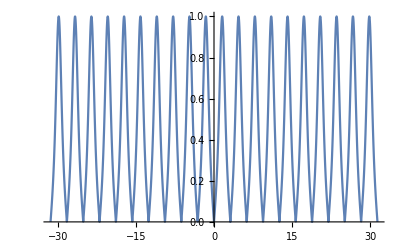

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-10 π,10 π}]
```

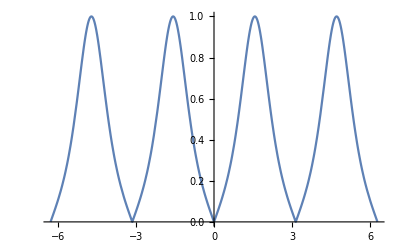

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-2 π,2π}]
```

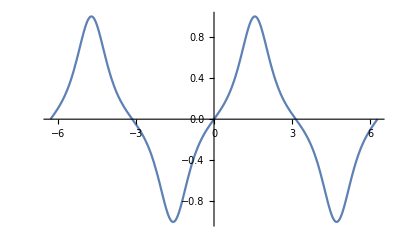

```mathematica
Plot[Sin[x]/((1+Cos[x]^2)^(3/2)),{x,-2 π,2π}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^3-x},x]==0,x∈Reals]
```

x==0

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x]==0,{x,f[x]}∈Reals]
```

√(f''[x]^2/((1+f'[x]^2)^3))==0

```mathematica
DSolve[√(f''[x]^2/((1+f'[x]^2)^3))==0,{f[x],f[x]},{x}]
```

{{f[x]→x C[1]+C[2]}}

```mathematica
FullSimplify[D[ArcCurvature[{x,f[x]},x],x]==0,{x,f[x]}∈Reals]
```

(-3 f'[x] f''[x]^3+(1+f'[x]^2) f''[x] f^(3)[x])/((1+f'[x]^2) √(f''[x]^2/((1+f'[x]^2)^3)))==0

```mathematica
DSolve[(-3 f'[x] f''[x]^3+(1+f'[x]^2) f''[x] Derivative[3][f][x])/((1+f'[x]^2) √(f''[x]^2/((1+f'[x]^2)^3)))==0,{f[x],f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]},{f[x]→-(ⅈ √(-1+x^2 C[1]^2+2 x C[1]^2 C[2]+C[1]^2 C[2]^2))/C[1]+C[3]},{f[x]→(ⅈ √(-1+x^2 C[1]^2+2 x C[1]^2 C[2]+C[1]^2 C[2]^2))/C[1]+C[3]}}

```mathematica
FullSimplify[DSolve[(-3 f'[x] f''[x]^3+(1+f'[x]^2) f''[x] Derivative[3][f][x])/((1+f'[x]^2) √(f''[x]^2/((1+f'[x]^2)^3)))==0,{f[x],f[x],f[x]},{x}],{x,f[x]}∈Reals]
```

{{f[x]→C[1]+x C[2]},{f[x]→-(ⅈ √(-1+C[1]^2 (x+C[2])^2))/C[1]+C[3]},{f[x]→(ⅈ √(-1+C[1]^2 (x+C[2])^2))/C[1]+C[3]}}

```mathematica
Binomial[3,3]
```

1

```mathematica
∑_(i=1)^n Binomial[n,n]
```

n

```mathematica
Binomial[0,0]
```

1

```mathematica
Binomial[0,1]
```

0

```mathematica
Normalize@{x,-y}
```

{x/(√(Abs[x]^2+Abs[y]^2)),-y/(√(Abs[x]^2+Abs[y]^2))}

```mathematica
FullSimplify[Normalize@{1,2x},x∈Reals]
```

{1/(√(1+4 x^2)),(2 x)/(√(1+4 x^2))}

```mathematica
FullSimplify[((2 x)/(√(1+4 x^2)))/(1/(√(1+4 x^2))),x∈Reals]
```

2 x

```mathematica
ArcTan[2 x]
```

ArcTan[2 x]

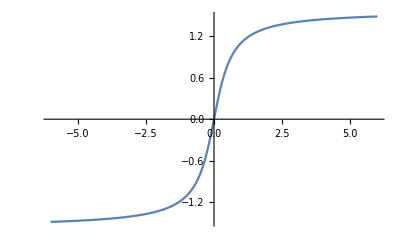

```mathematica
Plot[ArcTan[2 x],{x,-6.,6.}]
```

```mathematica
Abs@{x^3,x}
```

{Abs[x]^3,Abs[x]}

```mathematica
FullSimplify[Total@{Abs[x]^3,Abs[x]},x∈Reals]
```

Abs[x]+Abs[x]^3

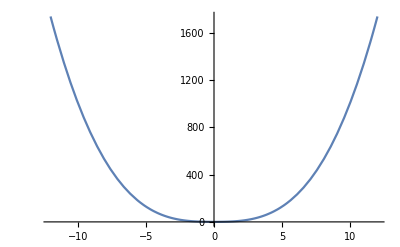

```mathematica
Plot[Abs[x]+Abs[x]^3,{x,-12.,12.}]
```

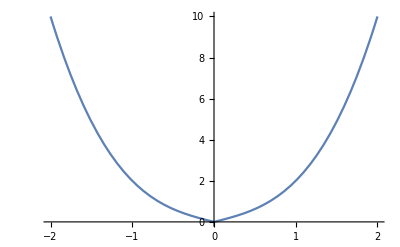

```mathematica
Plot[Abs[x]+Abs[x]^3,{x,-2,2}]
```

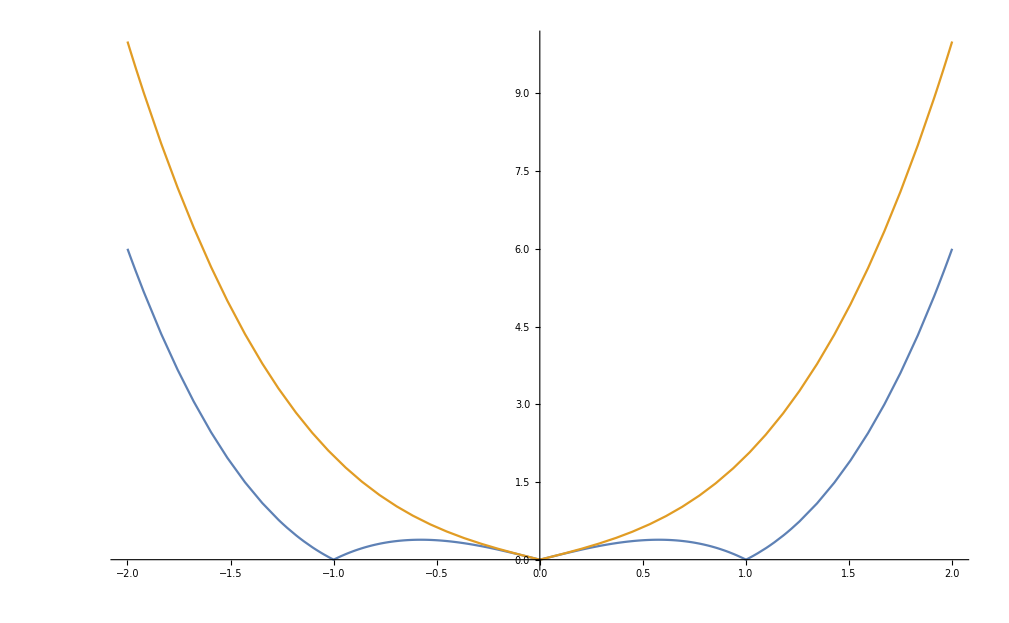

```mathematica
Plot[{Abs[x^3-x],Abs[x]+Abs[x]^3},{x,-2,2}]
```

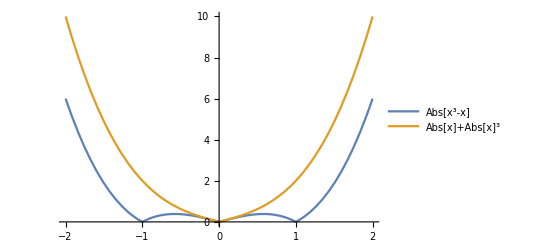

```mathematica
Plot[{Abs[x^3-x],Abs[x]+Abs[x]^3},{x,-2,2},PlotLegends->"Expressions"]
```

```mathematica
Normal@Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

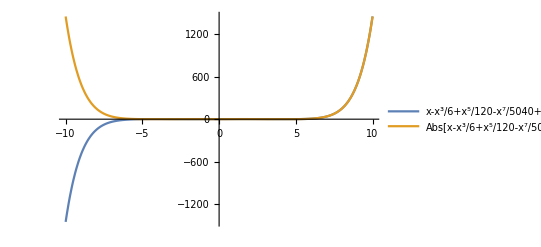

```mathematica
Plot[{x-x^3/6+x^5/120-x^7/5040+x^9/362880,Abs[x-x^3/6+x^5/120-x^7/5040+x^9/362880]},{x,-10,10},PlotRange->Full,PlotLegends->"Expressions",ImageSize->Full]
```

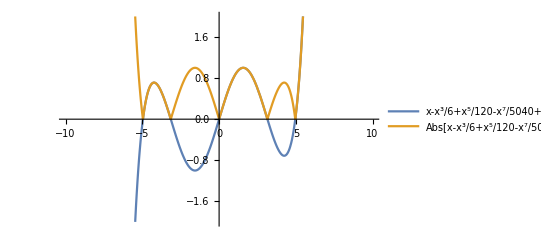

```mathematica
Plot[{x-x^3/6+x^5/120-x^7/5040+x^9/362880,Abs[x-x^3/6+x^5/120-x^7/5040+x^9/362880]},{x,-10,10},PlotRange->{-2,2},PlotLegends->"Expressions",ImageSize->Full]
```

```mathematica
x+x^5/120+x^9/362880-(x+x^3/6+x^7/5040)==0
```

-x^3/6+x^5/120-x^7/5040+x^9/362880==0

```mathematica
x+x^5/120+x^9/362880==(x+x^3/6+x^7/5040)
```

x+x^5/120+x^9/362880==x+x^3/6+x^7/5040

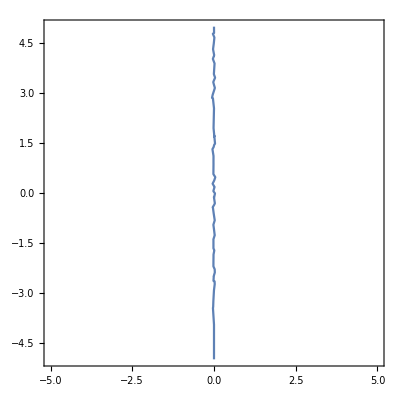

```mathematica
ContourPlot[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,{x,y}∈Disk[{0,0},5]]
```

```mathematica
Solve[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,x,Reals]
```

{{x→0},{x→0},{x→0},{x→Root-5.91Root[-60480+3024 #1^2-72 #1^4+#1^6&,1]-5.914295739849667},{x→Root5.91Root[-60480+3024 #1^2-72 #1^4+#1^6&,2]5.914295739849667}}

```mathematica
Solve[(x+x^5/120+x^9/362880)/x==(x+x^3/6+x^7/5040)/x,x,Reals]
```

{{x→0},{x→0},{x→Root-5.91Root[-60480+3024 #1^2-72 #1^4+#1^6&,1]-5.914295739849667},{x→Root5.91Root[-60480+3024 #1^2-72 #1^4+#1^6&,2]5.914295739849667}}

```mathematica
DivideSides[x,x+x^5/120+x^9/362880==x+x^3/6+x^7/5040]
```

DivideSides::eqin: x should be an equation or an inequality.

DivideSides[x,x+x^5/120+x^9/362880==x+x^3/6+x^7/5040]

```mathematica
DivideSides[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,x]
```

Piecewise[{{(x+x^5/120+x^9/362880)/x==(x+x^3/6+x^7/5040)/x, x≠0}, {x+x^5/120+x^9/362880==x+x^3/6+x^7/5040, True}}]

```mathematica
FullSimplify[DivideSides[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,x],x∈Reals]
```

x^3 (3024+x^4)==72 x (840+x^4)

```mathematica
FullSimplify[DivideSides[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,x^2],x∈Reals]
```

x^3 (3024+x^4)==72 x (840+x^4)

```mathematica
FullSimplify[DivideSides[x+x^5/120+x^9/362880==x+x^3/6+x^7/5040,x^3],x∈Reals]
```

x==0||x^2 (3024+x^4)==72 (840+x^4)